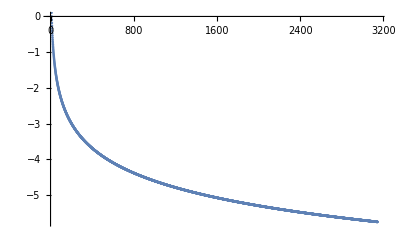

```mathematica
ListPlot[Table[- Log[x],{x,0,100*π,0.1}]]
```

```mathematica
Minimize[x Log[x],x]
```

{-1/ⅇ,{x→1/ⅇ}}

```mathematica
Show[{Graphics[{Red,PointSize[0.05], With[{p=1/ⅇ},Point[{p,p Log[p]}]]}],Plot[Callout[x Log[x],"Min",Below],{x,-3,3}]}, Axes->True]
```

-Graphics-

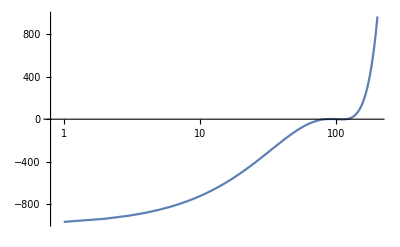

```mathematica
ListLogLinearPlot[Table[x^3-3x,{x,-10,10,0.1}],Joined->True]
```

```mathematica
Manipulate[With[{eqn=x^3-3 x},Show[Graphics[{Red,PointSize[0.04],Point[{p,eqn/.x->p}]},Axes->True,AspectRatio->1],Plot[eqn,{x,-3,3}]]],{{p,-1,"x"},-2,2}]
```

```mathematica
D[Subscript[x, 1]^2+Subscript[x, 2]^2,{{Subscript[x, 1],Subscript[x, 2]},2}]//PositiveSemidefiniteMatrixQ
```

True